# Convolution of two matrices

Faster Implementation using FFT via ListConvolve

```mathematica
(* Optimized Conv Product (Replaces the nested Do loops usinf FFT), see end of script for examples *)
JuryProductFFT[A_, B_] := ListConvolve[A, B, {1, 1}, 0]
```

```mathematica
(* Example 2: 3x3 matrices*)
A={{1,2,3,4},{4,5,6,7},{8,9,10,11}};
B={{10,11,12,13},{14,15,16,17},{18,19,20,21}};
(* MatrixForm[JuryProduct[A,B]]  Naive implementation*)
Print["J(",MatrixForm[A],", ",MatrixForm[B],") = ",MatrixForm[JuryProductFFT[A,B]]];
```

J((1 | 2 | 3 | 4
4 | 5 | 6 | 7
8 | 9 | 10 | 11), (10 | 11 | 12 | 13
14 | 15 | 16 | 17
18 | 19 | 20 | 21)) = (10 | 31 | 64 | 110
54 | 137 | 251 | 398
154 | 363 | 630 | 958)

Real Wishart Example

Generating Wishart matrices...

Computing eigenvalues...

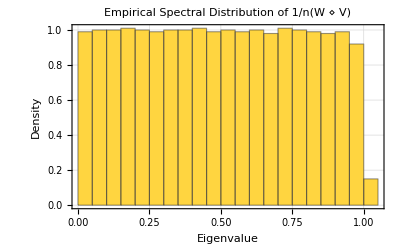

```mathematica
(* 1. Define a function to generate standard Wishart matrices *)
GenerateRealWishart[n_, p_] := Module[{X},
  X = RandomVariate[NormalDistribution[0, 1], {n, p}];
  (1/p) * X . Transpose[X]
]

(* 3. Set Dimensions (Keep n relatively small to start, e.g., 50 or 100) *)
(* 3. Set Dimensions to achieve γ = 1/2 *)
n = 2000;
d=n;
p=n;
(*gamma = 1/2;
d = Floor[Sqrt[n/gamma]];
p = d;*)
gamma = n/(d*p);
(* 4. Generate the independent Wishart matrices *)
Print["Generating Wishart matrices..."];
W = GenerateRealWishart[n, d];
V = GenerateRealWishart[n, p];

(* 5. Compute the scaled Jury product *)
Z = (1/n) * JuryProductFFT[W, V];

(* 6. Extract Eigenvalues *)
Print["Computing eigenvalues..."];
evals = Eigenvalues[Z];

(* 7. Plot the Empirical Spectral Distribution *)
(* 7. Plot the Empirical Spectral Distribution *)
Histogram[Re[evals], {0.05}, "PDF",
  PlotTheme -> "Detailed",
  PlotLabel -> Style["Empirical Spectral Distribution of \!\(\*FractionBox[\(1\), \(n\)]\)(W ⋄ V)", 14],
  AxesLabel -> {"Eigenvalue", "Density"},
  ChartStyle -> EdgeForm[GrayLevel[0.2]]
]
```

Generating Wishart matrices...

Computing Jury product...

Computing eigenvalues...

Generating Plot...

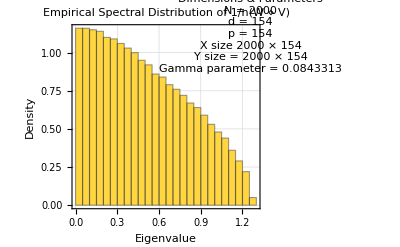

```mathematica
(* 1. Define a function to generate standard Wishart matrices *)
GenerateComplexWishart[n_, p_] := Module[{X},
  (* FIXED: Added 'I *' to properly generate a complex Gaussian matrix *)
  X = RandomVariate[NormalDistribution[0, 1], {n, p}] + 
      I * RandomVariate[NormalDistribution[0, 1], {n, p}];
  (1/(2 * p)) * X . ConjugateTranspose[X]
]

(* 2. Define the FFT Jury Product (From our earlier fix) *)
JuryProductFFT[A_, B_] := ListConvolve[A, B, {1, 1}, 0]

(* 3. Set Dimensions *)
n = 2000;

gammaTrue = 1/12;
d = Floor[Sqrt[n/gammaTrue]];
p = d;
gamma = n/(d*p);

(* Square Case 
p = n;
d = n;*)

(* 4. Generate the independent Wishart matrices *)
Print["Generating Wishart matrices..."];
W = GenerateComplexWishart[n, d];
V = GenerateComplexWishart[n, p];

(* 5. Compute the scaled Jury product *)
Print["Computing Jury product..."];
Z = (1/n) * JuryProductFFT[W, V];

(* 6. Extract Eigenvalues *)
Print["Computing eigenvalues..."];
evals = Eigenvalues[Z];

(* 7. Plot the Empirical Spectral Distribution with a Parameter Box *)
Print["Generating Plot..."];
Histogram[Re[evals], {0.05}, "PDF",
  PlotTheme -> "Detailed",
  PlotLabel -> Style["Empirical Spectral Distribution of \!\(\*FractionBox[\(1\), \(n\)]\)(W ⋄ V)", 14],
  AxesLabel -> {"Eigenvalue", "Density"},
  ChartStyle -> EdgeForm[GrayLevel[0.2]],
  
  (* --- ADDED EPILOG TO PUT TEXT INSIDE THE FIGURE --- *)
  Epilog -> Inset[
    Framed[
      Column[{
        Style["Dimensions & Parameters", Bold, 12],
        Row[{"N = ", n}],
        Row[{"d = ", d}],
        Row[{"p = ", p}],
        Row[{"X size ", n, " × ", d}],
        Row[{"Y size = ", n, " × ", p}],
        Row[{"Gamma parameter = ", N[gamma]}]
      }, Alignment -> Left, Spacings -> 0.5],
      Background -> Directive[White, Opacity[0.5]], (* Slight transparency *)
      FrameStyle -> GrayLevel[0.5],
      RoundingRadius -> 5
    ],
    Scaled[{0.95, 0.95}], (* Position inside the plot (Top-Right) *)
    Scaled[{1, 1}]        (* Alignment of the box (Top-Right corner of the box pins to the position) *)
  ]
]
```

## Permutations Computations

```mathematica
(*****************************************************************************
 * 
 * PROGRAM: Large N Asymptotic Exponent for Wishart Matrix Convolution
 * 
 * DESCRIPTION:
 * This script automates the calculation of the scaling exponent of N for 
 * given permutation pairs (tau, sigma) in S_k. It explicitly computes:
 *   1. The number of disjoint cycles in tau, sigma^{-1}*gamma_k, and 
 *      tau^{-1}*gamma_k (strictly accounting for 1-cycles/fixed points).
 *   2. The constraint matrix A_tau generated by the shift operator relations 
 *      Sum_{m \in c} (i_sigma(m) - i_m) = 0 along each cycle of tau.
 *   3. The degrees of freedom (nullity) of A_tau.
 *   4. The final topological exponent formula.
 * 
 * REASON / MATHEMATICAL CONTEXT:
 * You are evaluating the k-th moments of M_N, the convolution product of 
 * two independent N x N Wishart random matrices ( XX^* and YY^* ), represented 
 * via the Choi-Kraus map using forward shift operators F. 
 * 
 * When taking the expectation (1/N) E[Tr(M_N^k)], Wick's theorem expands 
 * the trace into a sum over two permutations sigma, tau in the symmetric 
 * group S_k. To find the large N limit (free probability regime), you must 
 * find which permutations maximize the power of N. The power of N depends on 
 * the cycle structure of the permutations and the geometric constraints 
 * forced by the shift operators on the trace indices. 
 * 
 * By plugging different permutations into this script, you can experimentally 
 * verify the upper bounds of the exponent (which should max out at 0) and 
 * identify the exact permutation pairs that contribute to the non-vanishing 
 * asymptotic moments (like non-crossing partitions).
 * 
 *****************************************************************************)
AnalyzePermutations[tau_, sigma_, k_] := Module[{
   gammaList, sigmaList, tauList, sigmaInvList, tauInvList,
   sigmaInvGammaList, tauInvGammaList, getCycles, tauCycles,
   numTau, numSigmaInvGamma, numTauInvGamma,
   buildRow, Atau, nullity, finalResult
  },
  
  (* 
     HELPER FUNCTION: getCycles
     Mathematica's default PermutationCycles[] hides 1-cycles (fixed points).
     Because our formula relies on counting ALL cycles (including singletons), 
     we write a custom function to extract the full disjoint cycle decomposition.
  *)
  getCycles[pList_] := Module[{unvisited = Range[Length[pList]], cycles = {}, curr, cycle},
   While[Length[unvisited] > 0,
    curr = First[unvisited];
    cycle = {};
    (* Follow the permutation map until we loop back to the start of the cycle *)
    While[MemberQ[unvisited, curr],
     AppendTo[cycle, curr];
     unvisited = DeleteCases[unvisited, curr];
     curr = pList[[curr]]; (* Move to the next element in the cycle *)
    ];
    AppendTo[cycles, cycle];
   ];
   cycles
  ];

  (* --- 1. SETUP PERMUTATION LISTS --- *)
  
  (* Create gamma_k = (1 2 3 ... k). As a list mapping i -> gamma(i), it is {2, 3, 4, ..., k, 1} *)
  gammaList = Append[Range[2, k], 1];
  
  (* Convert the input permutation objects into explicit mapping lists of length k *)
  sigmaList = PermutationList[sigma, k];
  tauList = PermutationList[tau, k];

  (* --- 2. INVERSES & COMPOSITIONS --- *)
  
  (* The inverse of a permutation list in Mathematica is found using Ordering[] *)
  sigmaInvList = Ordering[sigmaList];
  tauInvList = Ordering[tauList];

  (* 
     Composition of permutations: To compute f(g(x)), we apply the outer 
     list to the inner list. In Mathematica, this is simply fList[[gList]].
     Here we compute sigma^-1(gamma_k(x)) and tau^-1(gamma_k(x)).
  *)
  sigmaInvGammaList = sigmaInvList[[gammaList]];
  tauInvGammaList = tauInvList[[gammaList]];

  (* --- 3. COUNT CYCLES --- *)
  
  (* Extract the actual cycles of tau so we can build the matrix later *)
  tauCycles = getCycles[tauList];
  
  (* Count the number of cycles for each evaluated permutation *)
  numTau = Length[tauCycles];
  numSigmaInvGamma = Length[getCycles[sigmaInvGammaList]];
  numTauInvGamma = Length[getCycles[tauInvGammaList]];

  (* --- 4. CONSTRUCT THE SYSTEM MATRIX A_tau --- *)
  
  (* 
     For a single cycle c in tau, the equation is: Sum_{m in c} (i_sigma(m) - i_m) = 0.
     This helper function builds the corresponding row of coefficients for the matrix.
  *)
  buildRow[cycle_] := Module[{row = ConstantArray[0, k]},
   Do[
    row[[sigmaList[[m]]]] += 1; (* Coefficient +1 for i_sigma(m) *)
    row[[m]] -= 1;              (* Coefficient -1 for i_m *)
   , {m, cycle}];
   row
  ];
  
  (* Map the buildRow function over all cycles in tau to create the full matrix A_tau *)
  Atau = buildRow /@ tauCycles;

  (* --- 5. CALCULATE DEGREES OF FREEDOM --- *)
  
  (* By the Rank-Nullity Theorem, the number of free variables is k - rank(A_tau) *)
  nullity = k - MatrixRank[Atau];

  (* --- 6. EVALUATE THE FINAL FORMULA --- *)
  
  (* Calculate #(tau) + #(sigma^-1 gamma_k) + #(tau^-1 gamma_k) - 3k - 1 + (# free variables) *)
  finalResult = numTau + numSigmaInvGamma + numTauInvGamma - 3*k - 1 + nullity;

  (* --- 7. FORMAT OUTPUT --- *)
  
  (* Return a cleanly formatted grid containing all the intermediate variables and the final result *)
  Grid[{
    {Style["Parameter", Bold], Style["Value", Bold]},
    {"k", k},
    {"#(tau)", numTau},
    {"#(sigma^-1 gamma_k)", numSigmaInvGamma},
    {"#(tau^-1 gamma_k)", numTauInvGamma},
    {"Matrix A_tau", MatrixForm[Atau]},
    {"Free variables (nullity)", nullity},
    {"Formula Result", Style[finalResult, Bold, Red]}
   }, Frame -> All, Alignment -> {Left, Center}, Background -> {None, {LightGray, None}}]
]
```

```mathematica
tauInput = Cycles[{{1, 2, 3,4,7,6, 5,8}}];
sigmaInput = Cycles[{{1, 2, 3,4,5, 6, 7,8}}];

AnalyzePermutations[tauInput, sigmaInput, 8]
```

Parameter | Value
k | 8
#(tau) | 1
#(sigma^-1 gamma_k) | 8
#(tau^-1 gamma_k) | 6
Matrix A_tau | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
Free variables (nullity) | 8
Formula Result | -2

```mathematica
(* 
   GenerateRandomPermutations
   Input: k (Integer) - The size of the symmetric group S_k
   Output: A list containing two random permutations {sigma, tau}
*)
GenerateRandomPermutations[k_Integer] := Module[{sigma, tau},
  (* Generate two independent random permutations *)
  sigma = RandomPermutation[k];
  tau = RandomPermutation[k];
  
  (* Display the generated permutations clearly *)
  Print[Style["Random σ: ", Bold, Blue], sigma];
  Print[Style["Random τ: ", Bold, Blue], tau];
  
  (* Return them so they can be stored or passed to another function *)
  {sigma, tau}
]
```

```mathematica
(* Example 1*)
(* 1. Set the size of the symmetric group *)
k = 5;

(* 2. Generate the random pair *)
{randomSigma, randomTau} = GenerateRandomPermutations[k];

(* 3. Run the exact topological exponent analysis on the random pair *)
AnalyzePermutations[randomTau, randomSigma, k]
```

Random σ: Cycles[{{1,5,3}}]

Random τ: Cycles[{{2,3,4}}]

Parameter | Value
k | 5
#(tau) | 3
#(sigma^-1 gamma_k) | 1
#(tau^-1 gamma_k) | 3
Matrix A_tau | (-1 | 0 | 0 | 0 | 1
1 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | -1)
Free variables (nullity) | 3
Formula Result | -6

#### Testing all of them

```mathematica
(*****************************************************************************
 * 
 * PROGRAM: Global Exponent Distribution for All (sigma, tau) in S_K
 * 
 * DESCRIPTION:
 * This script loops through all (K!)^2 possible pairs of permutations in S_K.
 * To optimize speed, it replaces the manual cycle-counting loop with 
 * Mathematica's built-in PermutationCycles[], carefully adjusting to count 
 * 1-cycles (fixed points) which Mathematica normally hides.
 * 
 * Instead of printing millions of rows, it outputs a tally (frequency table) 
 * showing the distribution of the final calculated exponents. 
 * 
 * NOTE ON COMPLEXITY:
 * K = 4 -> 576 pairs (Instant)
 * K = 5 -> 14,400 pairs (Very Fast)
 * K = 6 -> 518,400 pairs (A few seconds)
 * K = 7 -> 25,401,600 pairs (May take a few minutes)
 * 
 *****************************************************************************)

TestAllPermutations[k_Integer] := Module[{
   perms, gammaList, resultsTally, totalPairs,
   sigmaList, tauList, sigmaInvList, tauInvList,
   sigmaInvGammaList, tauInvGammaList,
   numTau, numSigmaInvGamma, numTauInvGamma,
   tauCyclesList, allTauCycles, Atau, nullity, finalResult, 
   TotalCycles, buildRow
  },
  
  (* Generate all permutations of length k *)
  perms = Permutations[Range[k]];
  totalPairs = Length[perms]^2;
  gammaList = Append[Range[2, k], 1];
  
  (* We will store the frequency of each exponent here *)
  resultsTally = Association[];
  
  (* 
     HELPER: Efficiently count total cycles including 1-cycles.
     PermutationCycles returns Cycles[{{..}, {..}}]. We extract the lists,
     count the >1 cycles, and deduce the 1-cycles mathematically. 
  *)
  TotalCycles[pList_] := Module[{c = First[PermutationCycles[pList]]},
   Length[c] + k - Total[Length /@ c]
  ];

  (* Monitor displays a real-time progress bar while evaluating *)
  Monitor[
   (* Outer loop over sigma *)
   Do[
    sigmaList = perms[[i]];
    sigmaInvList = Ordering[sigmaList];
    sigmaInvGammaList = sigmaInvList[[gammaList]];
    numSigmaInvGamma = TotalCycles[sigmaInvGammaList];
    
    (* Inner loop over tau *)
    Do[
     tauList = perms[[j]];
     tauInvList = Ordering[tauList];
     tauInvGammaList = tauInvList[[gammaList]];
     
     numTau = TotalCycles[tauList];
     numTauInvGamma = TotalCycles[tauInvGammaList];
     
     (* 
        Construct the disjoint cycles for tau, explicitly including 1-cycles
        so we can build the matrix A_tau properly.
     *)
     tauCyclesList = First[PermutationCycles[tauList]];
     allTauCycles = Join[
       tauCyclesList,
       List /@ Complement[Range[k], Flatten[tauCyclesList]]
     ];
     
     (* Build Matrix A_tau rows *)
     buildRow[cycle_] := Module[{row = ConstantArray[0, k]},
      Do[
       row[[sigmaList[[m]]]] += 1;
       row[[m]] -= 1;
      , {m, cycle}];
      row
     ];
     
     Atau = buildRow /@ allTauCycles;
     
     (* Degrees of freedom *)
     nullity = k - MatrixRank[Atau];
     
     (* Final Evaluation *)
     finalResult = numTau + numSigmaInvGamma + numTauInvGamma - 3*k - 1 + nullity;
     
     (* Add to tally *)
     resultsTally[finalResult] = Lookup[resultsTally, finalResult, 0] + 1;
     
    , {j, 1, Length[perms]}];
   , {i, 1, Length[perms]}],
   
   (* Progress Bar UI *)
   Row[{"Processing σ ", i, " of ", Length[perms], 
        " (Total pairs: ", totalPairs, ")"}]
  ];
  
  (* Format the output as a beautiful table sorted by Exponent (highest to lowest) *)
  Grid[
   Prepend[
    Reverse[List @@@ Normal[KeySort[resultsTally]]], 
    {Style["Exponent (Power of N)", Bold], Style["Number of (σ, τ) Pairs", Bold]}
   ],
   Frame -> All, Alignment -> {Center, Center}, Background -> {None, {LightGray, None}}
  ]
]
```

```mathematica
(*Example 1*)
TestAllPermutations[6]
```

Exponent (Power of N) | Number of (σ, τ) Pairs
0 | 1
-1 | 45
-2 | 670
-3 | 4874
-4 | 20980
-5 | 59204
-6 | 112821
-7 | 142667
-8 | 113868
-9 | 52770
-10 | 10500

## Additional Code

### ListConvolve Examples

```mathematica
(*Example*)
Clear[a,b,c,d,e,f,x,y]
ListConvolve[{x, y}, {a, b, c, d, e, f}]
ListConvolve[{1,2},{1,2,3,4}]
```

{b x+a y,c x+b y,d x+c y,e x+d y,f x+e y}

{4,7,10}

```mathematica
(* Example *)
A={{1, 2}, {3, 4}};
B={{a, b}, {d, e}};
MatrixForm[ListConvolve[A, B]]
```

(4 a+3 b+2 d+e)

```mathematica
(* 2x2 Example*)
A={{1, 2}, {3, 4}};
B={{a, b}, {d, e}};
Print[MatrixForm[A]," and  ",MatrixForm[B]];
(* the 0 means padding *)
MatrixForm[ListConvolve[A, B, {1, 1}, 0]]
```

(1 | 2
3 | 4) and  (a | b
d | e)

```mathematica
(* 3x3 Example*)
A={{1, 2,3}, {4, 5,6}, {7, 8,9}};
B={{a, b,c}, {d, e,f},{g,h,i}};
Print[MatrixForm[A]," and  ",MatrixForm[B]];
MatrixForm[ListConvolve[A, B, {1, 1}, 0]]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9) and  (a | b | c
d | e | f
g | h | i)

(a | 2 a+b | 3 a+2 b+c
4 a+d | 5 a+4 b+2 d+e | 6 a+5 b+4 c+3 d+2 e+f
7 a+4 d+g | 8 a+7 b+5 d+4 e+2 g+h | 9 a+8 b+7 c+6 d+5 e+4 f+3 g+2 h+i)

```mathematica
(* 3x2 Example*)
F={{1, 2}, {4, 5}, {7, 8}};
G={{a, b}, {d, e},{g,h}};
Print[MatrixForm[F]," and  ",MatrixForm[G]];
MatrixForm[ListConvolve[F, G, {1, 1}, 0]]
```

(1 | 2
4 | 5
7 | 8) and  (a | b
d | e
g | h)

(a | 2 a+b
4 a+d | 5 a+4 b+2 d+e
7 a+4 d+g | 8 a+7 b+5 d+4 e+2 g+h)

```mathematica
(* Example: the 0 in the previous examples means padding, see what happens if its 1 *)
padding = 1;
F={{1, 2}, {4, 5}, {7, 8}};
G={{a, b}, {d, e},{g,h}};
Print[MatrixForm[F]," and  ",MatrixForm[G]];
MatrixForm[ListConvolve[F, G, {1, 1}, padding]]
```

(1 | 2
4 | 5
7 | 8) and  (a | b
d | e
g | h)

(26+a | 24+2 a+b
22+4 a+d | 15+5 a+4 b+2 d+e
15+7 a+4 d+g | 8 a+7 b+5 d+4 e+2 g+h)

```mathematica
(* Example: {1,1} *)
F={{1, 2}, {4, 5}, {7, 8}};
G={{a, b}, {d, e},{g,h}};
Print[MatrixForm[F]," and  ",MatrixForm[G]];
MatrixForm[ListConvolve[F, G, {-1, -1}, 0]]
```

(1 | 2
4 | 5
7 | 8) and  (a | b
d | e
g | h)

(8 a+7 b+5 d+4 e+2 g+h | 8 b+5 e+2 h
8 d+7 e+5 g+4 h | 8 e+5 h
8 g+7 h | 8 h)

## Naive Implementation

```mathematica
(* Old Implementation because its slow*)
Clear[JuryProduct]

(* 2. Define the Jury Product with a Progress Tracker for Rectangular Matrices *)
JuryProduct[A_, B_] := Module[{rows, cols, res, i, j},
  (* Get dimensions, ensuring we don't exceed the bounds of either matrix *)
  rows = Min[Length[A], Length[B]];
  cols = Min[Length[A[[1]]], Length[B[[1]]]];
  
  (* Pre-allocate with complex 0.0 to prevent performance loss from array unpacking *)
  res = ConstantArray[0.0 + 0.0 I, {rows, cols}];
  
  (* Monitor displays a dynamic progress bar during evaluation *)
  Monitor[
    Do[
      Do[
        (* Fast vectorized computation: slice, reverse B, multiply, and sum *)
        res[[i, j]] = Total[
          A[[1 ;; i, 1 ;; j]] * Reverse[B[[1 ;; i, 1 ;; j]], {1, 2}],
          2
        ],
        {j, 1, cols}
      ],
      {i, 1, rows}
    ],
    Row[{"Computing Jury Product: ", ProgressIndicator[i, {1, rows}], " (Row ", i, " of ", rows, ")"}]
  ];
  
  res
]
```

```mathematica
(* Example 1: 2x2 matrices*)
A = {{1,2},{3,4}};
MatrixForm[A];
MatrixForm[B];
B = {{5,6},{7,8}};
MatrixForm[JuryProduct[A,B]]
```

```mathematica
(* Example 2: 3x3 matrices*)
A={{1,2,3},{4,5,6},{7,8,9}};
B={{10,11,12},{13,14,15},{16,17,18}};
MatrixForm[JuryProduct[A,B]]
```

```mathematica
(* Example 3: 3x2 matrices*)
A={{1,2},{4,5},{7,8}};
B={{10,11},{13,14},{16,17}};
MatrixForm[JuryProduct[A,B]]
```